```mathematica
(* 绘图函数 *)
PlotG[number_]:={ParametricPlot[{Re[number],Im[number]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All,ImageSize->Medium]
Plot[{Re[number],Im[number]},{ξ,0,2π},PlotRange->All,ImageSize->Medium]
,Print["Stability interval length"->Re[number]/.ξ->π]};
termstop[k_]:=ⅇ^((k+1 )*ⅈ ξ)-ⅇ^(k*ⅈ ξ);
part={(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,2,2}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,3,3}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,4,4}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,5,5}])^2,(Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]-(-1)^(p+1)/p,{p,6,6}])^2};
```

```mathematica
Remove[k,o,R,f,bs,con,cons,β];
(*k是步数 o阶数 *)
(*k Количество шагов o порядка *)
k=3;o=2;
R=r/@Range[0,k];
f=Sum[r[s],{s,0,k}]==1;
(*sqrt*)
bs=Sum[r[s]^2,{s,0,k}];
(*高阶数条件 r[i]*)
(*Условие(высокого)порядка r[i]*)
con=Table[Total[Table[Total[Table[((s-1)^(p-1)+s^(p-1))r[m]r[m+s],{m,0,k-s}]],{s,1,k}]]==(-1)^(p+1)/p,{p,2,o}];
cons=Prepend[con,f];
(*r[i] решение*)
(*r[i] 求解*)
sol=NMinimize[{bs,cons},R,Method->Automatic,MaxIterations->250,WorkingPrecision->50,AccuracyGoal->25,PrecisionGoal->25];
(*β[k] решение*)
(*β[k] 求解*)
b=β/@Range[0,k];
bel=Reverse[(Table[Total[Table[{r[m]r[k-i+m]},{m,0,i}]],{i,0,k}]+Table[Total[Table[(-1)^(m-1)β[k-i+m],{m,1,i}]],{i,0,k}])];
c=Table[β[k-i]==bel[[k+1-i]],{i,0,k}]/.sol[[2]];
result=Solve[c,b]
α=Table[0,k+1];α[[k]]=1;α[[k+1]]=1;
σ[ξ_]:=∑_(i=0)^k result[[1,i+1,2]]*ξ^i;
Subscript[C, o+1]=(1/(o+1)!)(∑_(i=0)^k α[[i+1]]*i^(o+1)-(o+1)*∑_(i=0)^k result[[1,i+1,2]]*i^o);
C=Subscript[C, o+1]/σ[1];
{-Re[termstop[k]/Total[Table[result[[1,i+1,2]]*ⅇ^((k-i)ⅈ ξ),{i,0,k}]]]/.ξ->π,Subscript[C, o+1]/σ[1]}
```

{{β[0]→1.0251262658470763708529716469269187043893231016,β[1]→0.303300858899113726750405678928302590850558860375,β[2]→-0.181980515339456566059726574883636090824288529527,β[3]→-0.14644660940673353154365075097158520441559343245}}

Set::wrsym: Symbol C is Protected.

{1.4571067811865475244008444942415273225466974319 Re[termstop[3]],6.7046536768929904940240120230085876394268014082}

```mathematica
N[23/12]
N[-16/12]
N[5/12]
```

1.91667

-1.33333

0.416667

```mathematica
Rationalize[0.4166666666666667]
```

5/12

```mathematica
N[6/11]/100
```

0.00545455

```mathematica
Eigenvalues[{{-2000,999.75},{1,-2}}]
```

{-2000.5,-1.49975}

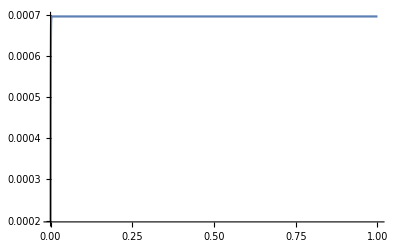

```mathematica
Plot[0.00099975-0.00049975*Exp[-2000.5*t]-0.0005*Exp[-0.5],{t,0,1},PlotRange->All]
```

```mathematica
N[5/12]
```

0.416667

```mathematica
Log[10,0.00012]
```

-3.92082

```mathematica
-Log[10,0.25]
```

0.60206

```mathematica
-Log[10,0.01]
```

2.